```mathematica
data = SemanticImport["data.csv"];
key = ToExpression/@data[[All,1;;-2]];
value = data[[All,-1]];
```

```mathematica
dataset = Table[Table[data[[n,x]],{x,12}]->data[[n,13]],{n,1,Length[data]}];
```

```mathematica
n=Length[dataset];
rs=RandomSample[Range[n]];
cut=Ceiling[.8 n];
train=dataset[[rs[[1;;cut]]]];
test=dataset[[rs[[cut+1;;]]]];
```

```mathematica
p=Predict[train,PerformanceGoal->"Quality"]
pm=PredictorMeasurements[p,test]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

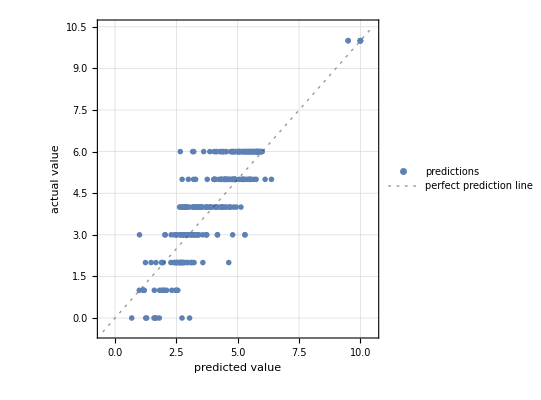

```mathematica
pm["ComparisonPlot"]
```

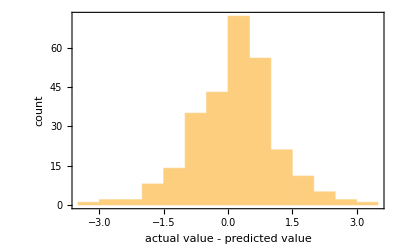

```mathematica
pm["ResidualHistogram"]
```

```mathematica
pm["StandardDeviation","Uncertainty"->True]
```

0.956±0.049

```mathematica
classifier=Classify[train,Method->"RandomForest"]
```

ClassifierFunction[…]

```mathematica
cm = ClassifierMeasurements[classifier,test]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.857143

```mathematica
accScores = {};
```

```mathematica
For[i=0,i<10,i++,
rs=RandomSample[Range[n]];
cut=Ceiling[.9 n];
train=dataset[[rs[[1;;cut]]]];
test=dataset[[rs[[cut+1;;]]]];
c=Classify[train,Method->"NeuralNetwork"];
AppendTo[accScores,ClassifierMeasurements[c,test,"Accuracy"]];
]
<|"folds_scores"->accScores,"avg_scores"->Mean[accScores]|>
```

<|folds_scores→{0.676471,0.514706,0.580882,0.580882,0.625,0.625,0.617647,0.647059,0.595588,0.617647},avg_scores→0.608088|>

```mathematica
accScores = {};
```

```mathematica
For[i=0,i<10,i++,
rs=RandomSample[Range[n]];
cut=Ceiling[.9 n];
train=dataset[[rs[[1;;cut]]]];
test=dataset[[rs[[cut+1;;]]]];
c=Classify[train,Method->"SupportVectorMachine"];
AppendTo[accScores,ClassifierMeasurements[c,test,"Accuracy"]];
]
<|"folds_scores"->accScores,"avg_scores"->Mean[accScores]|>
```

<|folds_scores→{0.647059,0.661765,0.654412,0.727941,0.676471,0.669118,0.632353,0.713235,0.610294,0.786765},avg_scores→0.677941|>

```mathematica
accScores = {};
```

```mathematica
For[i=0,i<10,i++,
rs=RandomSample[Range[n]];
cut=Ceiling[.9 n];
train=dataset[[rs[[1;;cut]]]];
test=dataset[[rs[[cut+1;;]]]];
c=Classify[train,Method->"NaiveBayes"];
AppendTo[accScores,ClassifierMeasurements[c,test,"Accuracy"]];
]
<|"folds_scores"->accScores,"avg_scores"->Mean[accScores]|>
```

<|folds_scores→{0.580882,0.544118,0.602941,0.536765,0.610294,0.625,0.566176,0.5,0.529412,0.522059},avg_scores→0.561765|>

```mathematica
accScores = {};
```

```mathematica
For[i=0,i<10,i++,
rs=RandomSample[Range[n]];
cut=Ceiling[.9 n];
train=dataset[[rs[[1;;cut]]]];
test=dataset[[rs[[cut+1;;]]]];
c=Classify[train,Method->"RandomForest"];
AppendTo[accScores,ClassifierMeasurements[c,test,"Accuracy"]];
]
<|"folds_scores"->accScores,"avg_scores"->Mean[accScores]|>
```

<|folds_scores→{0.845588,0.838235,0.875,0.911765,0.867647,0.867647,0.816176,0.845588,0.808824,0.860294},avg_scores→0.853676|>